```mathematica
Quit[]
```

```mathematica
Block[{hbar,m,alpha,lambda,Vx,qho},alpha=1;lambda=4;Vx=12*(1/2-1/Cosh[x]^2);

qho={-1/2*Laplacian[u[x],{x}]+Vx*u[x],DirichletCondition[u[x]==0,True]};
NDEigensystem[qho,u[x],{x,-10,10},4]]
```

Eigensystem::chnpdef: 警告：可能第一个参数中的第二个矩阵 SparseArray[«1»] 不是正定的，这对于用 Arnoldi 方法给出准确结果是必要的.

(0.210287 | 3.60839 | -3.66861 | 5.20477
InterpolatingFunction[{{-10., 10.}}, <>](x) | InterpolatingFunction[{{-10., 10.}}, <>](x) | InterpolatingFunction[{{-10., 10.}}, <>](x) | InterpolatingFunction[{{-10., 10.}}, <>](x))

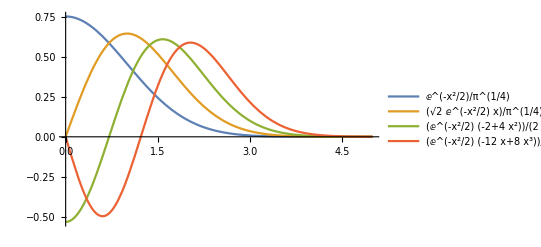

```mathematica
Block[{hbar,m,alpha,lambda,Vx,qho,eigens},alpha=1;lambda=4;Vx=1/2*alpha*x^2;

qho=-1/2*Laplacian[u[x],{x}]+Vx*u[x];
eigens=DEigensystem[qho,u[x],{x,-∞,∞},4,Method->"Normalize"];Plot[Evaluate[eigens[[2]]],{x,0,5},PlotLegends->"Expressions"]]
```